```mathematica
(*Transforma tensor vetorial de voigth em tensor  3x3*)
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
(*Transforma tensor  3x3 em tensor vetorial de voigth *)
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[2,3]],2sig[[1,3]],2sig[[1,2]]}
ComputeS[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
ComputeJ2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
ComputeI1[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
N[Tr[cart]]
]
P={{2/3,-1/3,-1/3,0,0,0},{-1/3,2/3,-1/3,0,0,0},{-1/3,-1/3,2/3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,2,0},{0,0,0,0,0,2}};
ax[sigma_]:=Sqrt[3]/(2 Sqrt[ComputeJ2[sigma]])ComputeS[sigma]
dadsigmax[sigma_]:=P Sqrt[3]/(2 Sqrt[ComputeJ2[sigma]])-Sqrt[3]/(4 ComputeJ2[sigma]^(3/2))Outer[Times,ComputeS[sigma],ComputeS[sigma]]
(*Calcula autovalores e autovetores e ordena na ordem decrescente*)
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];
F1HWCylVonMises[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy},
xiint=xi;
rhoint=Sqrt[2/3]sigy;
betaint=beta;
{xiint,rhoint,betaint}
]
FDP[I1_,J2_]:=Sqrt[3J2]-sigy;
ApplyStrainComputeSigmaDep[epst_,epsp_,subst2_]:=Block[{invCe,R,Q,invQ,sig1,sig2,sig3,epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,I1,J2,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},

Ce=N[{{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}}]//.subst2;
invCe=N[{{(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),0,0,0},{0,0,0,1/G,0,0},{0,0,0,0,1/G,0},{0,0,0,0,0,1/G}}]//.subst2;

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

epsetrial=(epstint-epspint);

sigma=Ce.epsetrial;

I1=ComputeI1[sigma];
J2=ComputeJ2[sigma];
yield=FDP[I1,J2]//.subst2;

If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,

xitrial=I1/Sqrt[3];
rhotrial=Sqrt[2J2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=ArcTan[(√3 (-sig2+sig3))/(-2 sig1+sig2+sig3)]//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
xisol=xitrial;
proj=HW[F1HWCylVonMises[{xisol,rho,betasol}]]//.subst2;
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
asol=ax[sigprojvoigth]//.subst2;
(*dadsigg=dadsigmax[sigprojvoigth]//.subst2;*)
epse=invCe.sigprojvoigth;
gamma=Norm[epsetrial-epse]/Norm[asol];

(*dadsigg=dadsigmax[sigma]//.subst2;
CT=Ce.((IdentityMatrix[6]-(Outer[Times,asol,asol].Ce)/(asol.Ce.asol)));
T=(IdentityMatrix[6]- gamma dadsigg.Ce );
Dep=CT.T;*)

dadsigg=dadsigmax[sigprojvoigth]//.subst2;
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
invQ=Inverse[Q];
R=invQ.Ce;
Dep= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];

];

Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
{sx,sy,tauxy}=sigproj2D;
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D,gamma}//.subst2

];
(*Compute2DShape*)
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[serendipity==True,
psis={
(1-xi)(1-eta)(-xi-eta-1)/4,(*1*)(1+xi)(1-eta)(xi-eta-1)/4,(*2*)(1+xi)(1+eta)(xi+eta-1)/4,(*3*)(1-xi)(1+eta)(-xi+eta-1)/4,(*4*)
(1-xi^2)(1-eta)/2,(*5*)(1+xi)(1-eta^2)/2,(*6*)(1-xi^2)(1+eta)/2,(*7*)(1-xi)(1-eta^2)/2(*8*)
};
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
(****************************************************************************************)
(*IntegrationRule*)
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
{pts,w}=Transpose[GaussianQuadratureWeights[porder+2,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
N[matpsts]
];
(****************************************************************************************)
(*CalcStiff*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob}
];
(*Compute one dimension shape functions*)
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
(*Find node id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]]-1,j]]=0;
Ek[[j,2ids[[i]]-1]]=0;
];
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=1;
Ef[[2ids[[i]]-1]]=val;
,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]],j]]=0;
Ek[[j,2ids[[i]]]]=0;
];
Ek[[2ids[[i]],2ids[[i]]]]=1;
Ef[[2ids[[i]]]]= val;
];
];
{Ek,Ef}
];
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

(*Compute a unitary normal vector wrt a circle o radius R*)
ComputeNormals[pt_,R_]:=Block[{lines,x,normal,v,delta=10^-9},
rr[x_]=-(x/Sqrt[R^2-(1-delta)x^2]);
pervec[v_]:={-(v[[2]]/Norm[v]),v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+pt[[2]];
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
];
(*Compute the force vector in a circle*)
ContributeLineNewmanPressure[nodes_,order_,ids_,R_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,normal,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
normal=ComputeNormals[pt,R];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,BB,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
BB={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];
(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)
{stress,Dep,epse,gamma}=ApplyStrainComputeSigmaDep[epst,epsp,subst2];
epspeint=epst-epse;
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
(*Element Stiffness Matrix contribution*)
ek=(Transpose[BB].Dep.BB)weight DetJ;
(*Element Internal force vector contribution*)
ef=(Transpose[BB].stress-Transpose[NShapes].{0,-bodyforce})weight DetJ;
{ek,ef}
];

(*CalcStiff - Assemble the element stiffness matrix and internal force vectors*)
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef}+=Contribute[data];
,{i,1,npts}
];
{ek,ef}
];

ComputeSolNoInterpolation[topol_,coords_,order_,coefs_,eltype_,scale_]:=Block[{elvecnorm,diplacenormvec,cx,cy,ux,uy,,displacevec,elvec,X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
displacevec={};
diplacenormvec={};
Table[
elvec={};
elvecnorm={};
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
cx=coords[[id,1]] ;
cy=coords[[id,2]] ;
ux=scale coefs[[2 id-1]] ;
 uy=scale coefs[[2id]] ;
AppendTo[elvec,{{cx,cy},{ux+cx,uy+cy}}];
AppendTo[elvecnorm,{cx,cy,Norm[{ux,uy}]}];
,{j,1,kk}];
AppendTo[displacevec,elvec];
AppendTo[diplacenormvec,elvec];
,{i,1,nels}];
{displacevec,diplacenormvec}
]

GenerateGridMesh[R0_,RE_,nx_,ny_,order_]:=Block[{x=0.,y=0.,dx,dy,meshnodes,i,j,meshtopology={},allcoords,k,l},
meshnodes={};
k=0;

(*meshnodes=Flatten[Table[Table[{R Cos[θ],R Sin[θ]},{R,R0,RE,(RE-R0)/(nx order-2)}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;*)
r=(RE/R0)^(1/(-2+nx order));
meshnodes=Flatten[Table[Table[{ R0 r^(n-1) Cos[θ], R0 r^(n-1) Sin[θ]},{n,1.,nx order-1}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;
k=0;
For[i=1 ,i<ny,i++,
l=1;
For[j=1,j<nx,j++,
(*AppendTo[meshtopology,{j+k,j+2+k,4 nx+j+k,4 nx-2+j+k,j+1+k,j+1+nx 2+k,j+nx 4-1+k,2 nx+ j-1+k,2 nx+ j+k}];*)
AppendTo[meshtopology,{l+k,l+2+k,4 nx+l+k,4 nx-2+l+k,l+1+k,l+1+nx 2+k,l+nx 4-1+k,2 nx+ l-1+k,2 nx+l+k}];
l+=2;
];
k+=4 nx-2;
];
If[order==2,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,9}];
,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,4}];
];
{allcoords,meshnodes,meshtopology}
]
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis},
If[order==2,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,5,2,6,3,7,4,8}]]]]}];
,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,2,3,4}]]]]}];
];
nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];
{meshvis,nodevis}
];
interpolatingQuadBezierCurve[pts_List]/;Length[pts]==3:=BezierCurve[{pts[[1]],1/2 (-pts[[1]]+4 pts[[2]]-pts[[3]]),pts[[3]]}];
interpolatingQuadBezierCurve[ptslist_List]:=interpolatingQuadBezierCurve/@ptslist;
interpolatingQuadBezierCurveComplex[coords_,indices_]:=interpolatingQuadBezierCurve[Map[coords[[#]]&,indices]]
GenerateGraphics[nodes_,topology_]:=Block[{meshvis,nodevis},
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->12]&,nodes],{PointSize[Large],Black,Point[nodes]}}];
Show[nodevis]]
DefineLinePath[pt0_,ptf_,n_]:=Block[{dy,cx0,cy0,cxf,cyf,R,RF,cx,cy,linecoords,deltax,deltay},


{cx0,cy0}=pt0;
{cxf,cyf}=ptf;

RF=Sqrt[cxf^2 + cyf^2];
R=Sqrt[cx0^2 + cy0^2];
Print[RF];
cx=cx0;
cy=cy0;

deltax=(cxf-cx0)/n;
deltay=(cyf-cy0)/n;
linecoords={};
Table[
AppendTo[linecoords,{cx,cy}];
cx+=deltax;
cy+=deltay;
,{i,1,n+1}];
linecoords
];
```

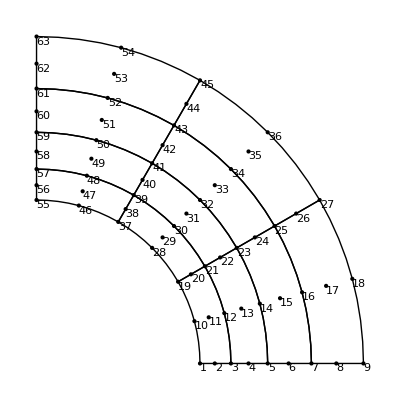

```mathematica
order=2;
serendipity=False;
{allcoords,nnodes,topol}=GenerateGridMesh[100,200,5,4,order];
linestopology=Flatten[Table[
{{topol[[i]][[1]],topol[[i]][[5]],topol[[i]][[2]]},
{topol[[i]][[2]],topol[[i]][[6]],topol[[i]][[3]]},
{topol[[i]][[3]],topol[[i]][[7]],topol[[i]][[4]]},
{topol[[i]][[4]],topol[[i]][[8]],topol[[i]][[1]]}
},{i,1,Length[topol]}],1];
Show[GenerateGraphics[nnodes,topol],Graphics[interpolatingQuadBezierCurveComplex[nnodes,linestopology]],ImageSize->Automatic]
x0=100;xf=200.;
y0=0;yf=0;
ndivs=100;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=100;yf=200;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
theta0=0;
thetaf=Pi/2;
r=100.;
searchpathinteriorhole=Table[{r Cos[theta],r Sin[theta]},{theta,theta0,thetaf,(thetaf-theta0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline];
idsleft=FindIds[nnodes,searchpathleftline];
idshole=FindIds[nnodes,searchpathinteriorhole];
```

```mathematica
planestress=False;
bodyforce=0;
ff=0.19209;
f[x_]:=ff;
fac={0.1/0.19209,0.14/0.19209,0.18/0.19209,0.19/0.19209,0.19209/0.19209}
FEXT=ContributeLineNewmanPressure[nnodes,order,idshole,r,f];
eltype=1;
order=2;
subst2={young->210,sigy->0.24,nu->0.3,G->young/(2(1+nu)),K->(young)/(3 (1-2nu))};
globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];
converge1={};
converge2={};
epspsolu={};
stresssolu={};
sol={};
solss={};
sol2={};
sol3={};
steps=10;
factor=1/steps;
displace=Table[0,{Length[nnodes] 2}];

lamb=1;
diff=10;
l=1;
counterout=1;
While[Abs[diff]>10^-6 && counterout≤30,
diverge=False;
convergevec1={};
convergevec2={};
Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;
temp=100;
tol=10^-6;
dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol,

epsppost={};
stressppost={};
globalcounter=1;
{KT,FINT}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
imposex=1;
imposey=2;

R=lamb  FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];
a=dwb.dwb;
b=2(dw+dws).dwb;
c=(dw+dws).(dw+dws)-l^2;
dlamb=Solve[a x^2 +b x+c==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];
AppendTo[convergevec1,{counter,err2}];
AppendTo[convergevec2,{counter,err1}];
Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[factor FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb];
counter++;
];
diff=Abs[lamb-lambn];
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];

AppendTo[converge1,convergevec1];
AppendTo[converge2,convergevec2];
AppendTo[sol,displace];
id=FindIds[nnodes,{{200,0}}][[1]];
AppendTo[sol2,{displace[[id 2-1]],ff lamb}];

(*AppendTo[sol2,{displace[[9 2-1]], ff fac[[i]]}];*)
AppendTo[sol3,epspvec];
factor+=1/steps;
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
];
```

{0.520589,0.728825,0.937061,0.98912,1.}

i = 1 | lamb = 1 | lambn = 0.998671 | diff = 10

Iteration number = 1  |R|/|FE| =  10.  |Δu|/|u| = 1.  |R| =  12.7299 |dw| = 1. | dlamb = -0.0937943 | lamb = 0.906206

Iteration number = 2  |R|/|FE| =  4.83646  |Δu|/|u| = 0.0120662  |R| =  6.15677 |dw| = 0.0120662 | dlamb = -0.117708 | lamb = 0.788497

Iteration number = 3  |R|/|FE| =  0.0666636  |Δu|/|u| = 0.000159144  |R| =  0.0848621 |dw| = 0.000159144 | dlamb = -0.000518333 | lamb = 0.787979

Iteration number = 4  |R|/|FE| =  0.0000149318  |Δu|/|u| = 4.11168×10^-8  |R| =  0.0000190081 |dw| = 4.11168×10^-8 | dlamb = -7.51465×10^-8 | lamb = 0.787979

i = 2 | lamb = 0.787979 | lambn = 1 | diff = 0.212021

Iteration number = 1  |R|/|FE| =  0.00287355  |Δu|/|u| = 0.500104  |R| =  0.007316 |dw| = 1. | dlamb = 0.40327 | lamb = 1.19125

Iteration number = 2  |R|/|FE| =  3.72946  |Δu|/|u| = 0.0137344  |R| =  9.49513 |dw| = 0.0274568 | dlamb = -0.207603 | lamb = 0.983647

Iteration number = 3  |R|/|FE| =  0.0595716  |Δu|/|u| = 0.00022527  |R| =  0.151668 |dw| = 0.000450342 | dlamb = -0.000962511 | lamb = 0.982684

Iteration number = 4  |R|/|FE| =  0.0000118017  |Δu|/|u| = 7.07029×10^-7  |R| =  0.0000300468 |dw| = 1.41344×10^-6 | dlamb = -1.35269×10^-7 | lamb = 0.982684

i = 3 | lamb = 0.982684 | lambn = 0.787979 | diff = 0.194705

Iteration number = 1  |R|/|FE| =  0.0143743  |Δu|/|u| = 0.352462  |R| =  0.0548952 |dw| = 1. | dlamb = 0.0501853 | lamb = 1.03287

Iteration number = 2  |R|/|FE| =  1.15378  |Δu|/|u| = 0.122753  |R| =  4.40627 |dw| = 0.36343 | dlamb = -0.0327031 | lamb = 1.00017

Iteration number = 3  |R|/|FE| =  0.0556142  |Δu|/|u| = 0.104326  |R| =  0.212389 |dw| = 0.312824 | dlamb = -0.000471596 | lamb = 0.999695

Iteration number = 4  |R|/|FE| =  0.00648517  |Δu|/|u| = 0.00791989  |R| =  0.0247667 |dw| = 0.0237496 | dlamb = -0.0000428227 | lamb = 0.999652

Iteration number = 5  |R|/|FE| =  0.0000348196  |Δu|/|u| = 0.0000411779  |R| =  0.000132975 |dw| = 0.000123481 | dlamb = -2.33164×10^-7 | lamb = 0.999651

Iteration number = 6  |R|/|FE| =  1.57428×10^-9  |Δu|/|u| = 2.40426×10^-9  |R| =  6.01215×10^-9 |dw| = 7.20972×10^-9 | dlamb = -9.85826×10^-12 | lamb = 0.999651

i = 4 | lamb = 0.999651 | lambn = 0.982684 | diff = 0.0169675

Iteration number = 1  |R|/|FE| =  0.0317143  |Δu|/|u| = 0.250089  |R| =  0.161488 |dw| = 1. | dlamb = 0.0042729 | lamb = 1.00392

Iteration number = 2  |R|/|FE| =  0.136388  |Δu|/|u| = 0.000672429  |R| =  0.694482 |dw| = 0.00268873 | dlamb = -0.00395253 | lamb = 0.999972

Iteration number = 3  |R|/|FE| =  0.0000917422  |Δu|/|u| = 5.18976×10^-6  |R| =  0.000467148 |dw| = 0.0000207514 | dlamb = -5.08099×10^-6 | lamb = 0.999967

Iteration number = 4  |R|/|FE| =  8.17328×10^-9  |Δu|/|u| = 9.88639×10^-10  |R| =  4.16181×10^-8 |dw| = 3.95311×10^-9 | dlamb = -2.26659×10^-12 | lamb = 0.999967

i = 5 | lamb = 0.999967 | lambn = 0.999651 | diff = 0.000315284

Iteration number = 1  |R|/|FE| =  0.0334065  |Δu|/|u| = 0.200062  |R| =  0.212631 |dw| = 1. | dlamb = 0.00396398 | lamb = 1.00393

Iteration number = 2  |R|/|FE| =  0.109373  |Δu|/|u| = 0.000534828  |R| =  0.696156 |dw| = 0.0026733 | dlamb = -0.0039534 | lamb = 0.999977

Iteration number = 3  |R|/|FE| =  0.0000737648  |Δu|/|u| = 3.58932×10^-6  |R| =  0.000469509 |dw| = 0.0000179409 | dlamb = -5.06376×10^-6 | lamb = 0.999972

Iteration number = 4  |R|/|FE| =  6.51533×10^-9  |Δu|/|u| = 7.90141×10^-10  |R| =  4.14698×10^-8 |dw| = 3.94946×10^-9 | dlamb = -2.16429×10^-12 | lamb = 0.999972

i = 6 | lamb = 0.999972 | lambn = 0.999967 | diff = 5.52314×10^-6

Iteration number = 1  |R|/|FE| =  0.027965  |Δu|/|u| = 0.166712  |R| =  0.213595 |dw| = 1. | dlamb = 0.00395896 | lamb = 1.00393

Iteration number = 2  |R|/|FE| =  0.0911599  |Δu|/|u| = 0.000444897  |R| =  0.696274 |dw| = 0.00266864 | dlamb = -0.00395366 | lamb = 0.999978

Iteration number = 3  |R|/|FE| =  0.0000614811  |Δu|/|u| = 2.8094×10^-6  |R| =  0.000469589 |dw| = 0.0000168517 | dlamb = -5.0576×10^-6 | lamb = 0.999972

Iteration number = 4  |R|/|FE| =  5.42228×10^-9  |Δu|/|u| = 6.5869×10^-10  |R| =  4.14151×10^-8 |dw| = 3.95105×10^-9 | dlamb = -2.11761×10^-12 | lamb = 0.999972

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

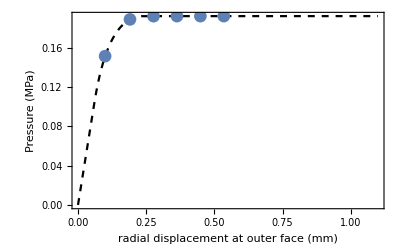

```mathematica
data=Table[i,{i,0,0.192,0.001}];
Clear[f]
eq[P_]:=(Log[c/a]+0.5 (1-c^2/b^2))-P/Y;
ub0[P_]:=2 P b/(young (b^2/a^2-1))(1-nu^2);
ub1[c_]:=Y c^2 (1-nu^2)/(young b);
Clear[a,b,c,nu,sigy,young]
subst={Y->2 sigy/Sqrt[3],young->210, b->200,a->100,sigy->0.240,nu->0.3};
P0=Y/2 (1 - a^2 /b^2) //.subst;
f[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,0.2}][[1,2]];
solu=ub1[solc]//.subst;
solu
]
computec[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,100}][[1,2]]
]
ComputeAnalyticalStress[r_,P_]:=Block[{a=100,b=200,sigy=0.24,sigr,sigt,cc,Y},
Y=2 sigy/Sqrt[3];
cc=computec[P];
If[a<=r<=cc,
sigr=Y(-0.5 -Log[cc/r]+cc^2 /(2 b^2));
sigt=Y(0.5 -Log[cc/r]+cc^2 /(2 b^2));
];
If[cc<=r≤b,
sigr=-Y cc^2 /(2 b^2)(b^2 / r^2 -1);
sigt=Y cc^2 /(2 b^2)(b^2 / r^2 +1);
];
{sigr,sigt}
]
u[P_]:=If[P<P0,ub0[P],f[P]]
tab=Table[{u[data[[i]]]//.subst ,data[[i]]},{i,1,Length[data]}];
AppendTo[tab,{0.3,0.19208}];
AppendTo[tab,{1.1,0.19208}];
a=ListLinePlot[tab,PlotStyle->{Black,Dashed}];
b=ListPlot[sol2,PlotMarkers->{Automatic,13}];
Show[a,b,PlotRange->All,PlotLegends->Placed[{"Analytical Solution", "Present Solution"},{0.79,0.11}],Frame->True,FrameLabel->{"radial displacement at outer face (mm)","Pressure (MPa)"}]
```

{{375.,500.},{250.,500.},{250.,475.},{375.,462.5},{312.5,500.},{250.,487.5},{312.5,470.438},{375.,481.25}}

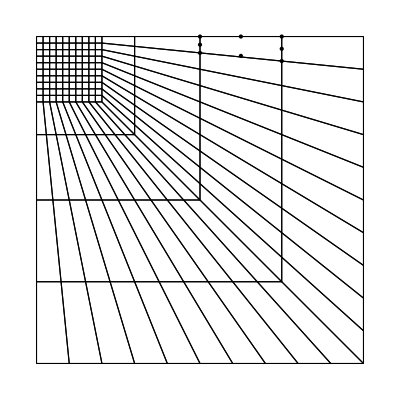

2

{1,3,5,6,10,13,16,20,25,33,39,46,53,62,69,84,94,109,124,140,155}

{155,160,173,189,211,240,313,364,430,444,454,471,480,496,504,519,526,538,544,554,559,566,570,576,579,583,585,587,589}

{543,553,558,567,571,577,580,584,586,588,589}

{1,2,4,7,9,14,15,19,24,32,38,45,54,61,70,85,95,110,123,139,154}

```mathematica
pack=Developer`ToPackedArray;

topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/setx566dvgx3urx/mesh-els-strip-foot-structured4.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/mxelbdwug4yv3lr/mesh-nodes-strip-foot-structured4.txt?dl=1","Table"];
(*topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/gz1rastmoemiaz0/mesh-els-strip-foot-structured-ninenode.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/vaz8ljhr79hxpnt/mesh-nodes-strip-foot-structured-ninenode.txt?dl=1","Table"];*)

nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nnodes]}}];
Show[meshVis1];
el=60;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]
order=2
serendipity=False;

a=500;
b2=50;
x0=0.;xf=a;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=a;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=0;xf=b2;
y0=a;yf=a;
searchpathupline=Table[{x,y0},{x,x0,xf,(xf-x0)/ndivs}];
x0=a;xf=a;
y0=0;yf=a;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idssup=FindIds[nnodes,searchpathupline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


subst2={young->10000000.,sigy->848.7,nu->0.48,G->young/(2(1+nu)),K->(young)/(3 (1-2nu))};


f[x_]:=2.97 sigy//.subst2 ;
FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};

lamb=1;
diff=10;
l=0.3;
counterout=1;
tol1=10^-3;
tol2=10^-6;
While[Abs[diff]>tol1 && counterout≤30,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol2,

epsppost={};
stressppost={};
globalcounter=1;
{KT,FINT}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
imposex=1;
imposey=2;

R=lamb  FEXT-FINT;

{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];
a=dwb.dwb;
b=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
dlamb=Solve[a x^2 +b x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];
AppendTo[convergevec1,{counter,err2}];
AppendTo[convergevec2,{counter,err1}];
Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[factor FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb];
counter++;
];
diff=Abs[lamb-lambn];
cc=sigy/Sqrt[3]//.subst2;
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];

AppendTo[converge1,convergevec1];
AppendTo[converge2,convergevec2];
AppendTo[sol,displace];
id=FindIds[nnodes,{{0,500}}][[1]];
AppendTo[sol2,{-displace[[id 2]]/100, f[x] lamb/cc}];

(*AppendTo[sol2,{displace[[9 2-1]], ff fac[[i]]}];*)
AppendTo[sol3,epspvec];
factor+=1/steps;
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

i = 1 | lamb = 1 | lambn = 1.04289 | diff = 10

Iteration number = 1  |R|/|FE| =  0.37037  |Δu|/|u| = 1.  |R| =  41588.4 |dw| = 0.3 | dlamb = -0.1259 | lamb = 0.8741

Iteration number = 2  |R|/|FE| =  0.0520293  |Δu|/|u| = 0.131939  |R| =  5842.31 |dw| = 0.0395818 | dlamb = -0.0796286 | lamb = 0.794472

Iteration number = 3  |R|/|FE| =  0.0427984  |Δu|/|u| = 0.0236169  |R| =  4805.78 |dw| = 0.00708507 | dlamb = -0.0106619 | lamb = 0.78381

Iteration number = 4  |R|/|FE| =  0.00885296  |Δu|/|u| = 0.00227805  |R| =  994.087 |dw| = 0.000683414 | dlamb = -0.000832209 | lamb = 0.782978

Iteration number = 5  |R|/|FE| =  0.000470151  |Δu|/|u| = 0.000055369  |R| =  52.7927 |dw| = 0.0000166107 | dlamb = -0.0000141775 | lamb = 0.782963

Iteration number = 6  |R|/|FE| =  2.32443×10^-7  |Δu|/|u| = 7.74321×10^-8  |R| =  0.0261007 |dw| = 2.32296×10^-8 | dlamb = -1.96909×10^-8 | lamb = 0.782963

i = 2 | lamb = 0.782963 | lambn = 1 | diff = 0.217037

Iteration number = 1  |R|/|FE| =  0.000221269  |Δu|/|u| = 0.515518  |R| =  25.7662 |dw| = 0.3 | dlamb = 0.3296 | lamb = 1.11256

Iteration number = 2  |R|/|FE| =  0.243477  |Δu|/|u| = 0.0778848  |R| =  28352.3 |dw| = 0.0447193 | dlamb = -0.14426 | lamb = 0.968303

Iteration number = 3  |R|/|FE| =  0.101212  |Δu|/|u| = 0.0181642  |R| =  11785.9 |dw| = 0.0104196 | dlamb = -0.00656479 | lamb = 0.961738

Iteration number = 4  |R|/|FE| =  0.0151084  |Δu|/|u| = 0.0029875  |R| =  1759.34 |dw| = 0.00171322 | dlamb = -0.00101586 | lamb = 0.960722

Iteration number = 5  |R|/|FE| =  0.00175863  |Δu|/|u| = 0.000373446  |R| =  204.788 |dw| = 0.000214152 | dlamb = -0.0000656955 | lamb = 0.960657

Iteration number = 6  |R|/|FE| =  0.000230101  |Δu|/|u| = 0.000029517  |R| =  26.7947 |dw| = 0.0000169265 | dlamb = -1.37073×10^-6 | lamb = 0.960655

Iteration number = 7  |R|/|FE| =  2.20441×10^-7  |Δu|/|u| = 3.15243×10^-8  |R| =  0.0256698 |dw| = 1.80776×10^-8 | dlamb = -2.20716×10^-9 | lamb = 0.960655

i = 3 | lamb = 0.960655 | lambn = 0.782963 | diff = 0.177692

Iteration number = 1  |R|/|FE| =  0.000569024  |Δu|/|u| = 0.347308  |R| =  68.628 |dw| = 0.3 | dlamb = 0.122538 | lamb = 1.08319

Iteration number = 2  |R|/|FE| =  0.133753  |Δu|/|u| = 0.0407192  |R| =  16131.4 |dw| = 0.0348851 | dlamb = -0.0507258 | lamb = 1.03247

Iteration number = 3  |R|/|FE| =  0.0299102  |Δu|/|u| = 0.0156691  |R| =  3607.36 |dw| = 0.0133874 | dlamb = -0.00482801 | lamb = 1.02764

Iteration number = 4  |R|/|FE| =  0.00732958  |Δu|/|u| = 0.00544746  |R| =  883.994 |dw| = 0.00465 | dlamb = -0.000886252 | lamb = 1.02675

Iteration number = 5  |R|/|FE| =  0.000424597  |Δu|/|u| = 0.000242556  |R| =  51.2092 |dw| = 0.000207041 | dlamb = -0.0000310913 | lamb = 1.02672

Iteration number = 6  |R|/|FE| =  2.86463×10^-6  |Δu|/|u| = 1.34618×10^-6  |R| =  0.345493 |dw| = 1.14907×10^-6 | dlamb = -1.41458×10^-7 | lamb = 1.02672

Iteration number = 7  |R|/|FE| =  3.75206×10^-10  |Δu|/|u| = 1.43304×10^-10  |R| =  0.0000452522 |dw| = 1.22322×10^-10 | dlamb = -1.25447×10^-11 | lamb = 1.02672

i = 4 | lamb = 1.02672 | lambn = 0.960655 | diff = 0.0660668

Iteration number = 1  |R|/|FE| =  0.000675517  |Δu|/|u| = 0.265846  |R| =  84.2811 |dw| = 0.3 | dlamb = 0.050094 | lamb = 1.07682

Iteration number = 2  |R|/|FE| =  0.0841875  |Δu|/|u| = 0.0696681  |R| =  10503.7 |dw| = 0.0765108 | dlamb = -0.0372615 | lamb = 1.03955

Iteration number = 3  |R|/|FE| =  0.0264165  |Δu|/|u| = 0.0174054  |R| =  3295.86 |dw| = 0.0190354 | dlamb = -0.00187899 | lamb = 1.03768

Iteration number = 4  |R|/|FE| =  0.00312665  |Δu|/|u| = 0.00402609  |R| =  390.098 |dw| = 0.00439772 | dlamb = -0.00032272 | lamb = 1.03735

Iteration number = 5  |R|/|FE| =  0.000178991  |Δu|/|u| = 0.000204971  |R| =  22.3319 |dw| = 0.000223876 | dlamb = -0.0000159999 | lamb = 1.03734

Iteration number = 6  |R|/|FE| =  6.23614×10^-7  |Δu|/|u| = 8.38756×10^-7  |R| =  0.0778053 |dw| = 9.16119×10^-7 | dlamb = -5.80146×10^-8 | lamb = 1.03734

i = 5 | lamb = 1.03734 | lambn = 1.02672 | diff = 0.0106147

Iteration number = 1  |R|/|FE| =  0.000688606  |Δu|/|u| = 0.21704  |R| =  88.7779 |dw| = 0.3 | dlamb = 0.0544544 | lamb = 1.09179

Iteration number = 2  |R|/|FE| =  0.0987442  |Δu|/|u| = 0.0888203  |R| =  12730.5 |dw| = 0.119165 | dlamb = -0.0489727 | lamb = 1.04282

Iteration number = 3  |R|/|FE| =  0.0371653  |Δu|/|u| = 0.00363788  |R| =  4791.51 |dw| = 0.00488858 | dlamb = -0.00100141 | lamb = 1.04182

Iteration number = 4  |R|/|FE| =  0.0041951  |Δu|/|u| = 0.00109238  |R| =  540.85 |dw| = 0.00146867 | dlamb = -0.0000366417 | lamb = 1.04178

Iteration number = 5  |R|/|FE| =  0.000623132  |Δu|/|u| = 0.000110298  |R| =  80.3368 |dw| = 0.0001483 | dlamb = -1.13017×10^-8 | lamb = 1.04178

Iteration number = 6  |R|/|FE| =  0.000021019  |Δu|/|u| = 1.6808×10^-6  |R| =  2.70986 |dw| = 2.2599×10^-6 | dlamb = 1.02567×10^-8 | lamb = 1.04178

Iteration number = 7  |R|/|FE| =  3.01509×10^-10  |Δu|/|u| = 4.33142×10^-11  |R| =  0.0000388718 |dw| = 5.82375×10^-11 | dlamb = -1.25962×10^-12 | lamb = 1.04178

i = 6 | lamb = 1.04178 | lambn = 1.03734 | diff = 0.00444366

Iteration number = 1  |R|/|FE| =  0.000714554  |Δu|/|u| = 0.183124  |R| =  95.0949 |dw| = 0.3 | dlamb = 0.045592 | lamb = 1.08737

Iteration number = 2  |R|/|FE| =  0.0699366  |Δu|/|u| = 0.0685521  |R| =  9307.36 |dw| = 0.110251 | dlamb = -0.042332 | lamb = 1.04504

Iteration number = 3  |R|/|FE| =  0.0217163  |Δu|/|u| = 0.00373587  |R| =  2890.08 |dw| = 0.00600831 | dlamb = -0.000732794 | lamb = 1.04431

Iteration number = 4  |R|/|FE| =  0.00297337  |Δu|/|u| = 0.000611979  |R| =  395.704 |dw| = 0.000984253 | dlamb = -0.0000471924 | lamb = 1.04426

Iteration number = 5  |R|/|FE| =  0.00042761  |Δu|/|u| = 0.0000630757  |R| =  56.9077 |dw| = 0.000101445 | dlamb = -2.35843×10^-6 | lamb = 1.04426

Iteration number = 6  |R|/|FE| =  7.36779×10^-7  |Δu|/|u| = 3.83175×10^-7  |R| =  0.0980528 |dw| = 6.16266×10^-7 | dlamb = -1.35353×10^-8 | lamb = 1.04426

i = 7 | lamb = 1.04426 | lambn = 1.04178 | diff = 0.00247768

Iteration number = 1  |R|/|FE| =  0.000739871  |Δu|/|u| = 0.157683  |R| =  101.541 |dw| = 0.3 | dlamb = 0.0916212 | lamb = 1.13588

Iteration number = 2  |R|/|FE| =  0.173907  |Δu|/|u| = 0.0668491  |R| =  23867.3 |dw| = 0.126767 | dlamb = -0.0819311 | lamb = 1.05395

Iteration number = 3  |R|/|FE| =  0.0468744  |Δu|/|u| = 0.0302831  |R| =  6433.13 |dw| = 0.0571174 | dlamb = -0.00563195 | lamb = 1.04832

Iteration number = 4  |R|/|FE| =  0.0132144  |Δu|/|u| = 0.00923638  |R| =  1813.56 |dw| = 0.0173824 | dlamb = -0.00170894 | lamb = 1.04661

Iteration number = 5  |R|/|FE| =  0.00307716  |Δu|/|u| = 0.0036982  |R| =  422.314 |dw| = 0.00695299 | dlamb = -0.000681847 | lamb = 1.04593

Iteration number = 6  |R|/|FE| =  0.000703473  |Δu|/|u| = 0.000273158  |R| =  96.5459 |dw| = 0.00051353 | dlamb = -0.0000735502 | lamb = 1.04585

Iteration number = 7  |R|/|FE| =  6.46905×10^-6  |Δu|/|u| = 2.59054×10^-6  |R| =  0.887823 |dw| = 4.87015×10^-6 | dlamb = -5.43425×10^-7 | lamb = 1.04585

Iteration number = 8  |R|/|FE| =  2.91589×10^-10  |Δu|/|u| = 2.05549×10^-10  |R| =  0.0000400182 |dw| = 3.86427×10^-10 | dlamb = -4.06121×10^-11 | lamb = 1.04585

i = 8 | lamb = 1.04585 | lambn = 1.04426 | diff = 0.00159327

Iteration number = 1  |R|/|FE| =  0.000757869  |Δu|/|u| = 0.137727  |R| =  107.163 |dw| = 0.3 | dlamb = 0.0518682 | lamb = 1.09772

Iteration number = 2  |R|/|FE| =  0.0857468  |Δu|/|u| = 0.0577525  |R| =  12124.6 |dw| = 0.124563 | dlamb = -0.0499193 | lamb = 1.0478

Iteration number = 3  |R|/|FE| =  0.0222232  |Δu|/|u| = 0.00318649  |R| =  3142.37 |dw| = 0.00687377 | dlamb = -0.000744451 | lamb = 1.04706

Iteration number = 4  |R|/|FE| =  0.00351271  |Δu|/|u| = 0.00104087  |R| =  496.7 |dw| = 0.00224523 | dlamb = -0.0000849335 | lamb = 1.04697

Iteration number = 5  |R|/|FE| =  0.000601372  |Δu|/|u| = 0.000247881  |R| =  85.0344 |dw| = 0.00053468 | dlamb = -8.57288×10^-6 | lamb = 1.04696

Iteration number = 6  |R|/|FE| =  0.0000174451  |Δu|/|u| = 9.41336×10^-6  |R| =  2.46675 |dw| = 0.0000203047 | dlamb = -3.30196×10^-7 | lamb = 1.04696

Iteration number = 7  |R|/|FE| =  2.16161×10^-8  |Δu|/|u| = 1.22339×10^-8  |R| =  0.00305653 |dw| = 2.63886×10^-8 | dlamb = -4.4452×10^-10 | lamb = 1.04696

i = 9 | lamb = 1.04696 | lambn = 1.04585 | diff = 0.00111056

Iteration number = 1  |R|/|FE| =  0.000776271  |Δu|/|u| = 0.122239  |R| =  112.994 |dw| = 0.3 | dlamb = 0.0698147 | lamb = 1.11678

Iteration number = 2  |R|/|FE| =  0.12568  |Δu|/|u| = 0.0681038  |R| =  18294. |dw| = 0.165666 | dlamb = -0.0679442 | lamb = 1.04883

Iteration number = 3  |R|/|FE| =  0.0366473  |Δu|/|u| = 0.00386714  |R| =  5334.36 |dw| = 0.00941934 | dlamb = -0.000897187 | lamb = 1.04794

Iteration number = 4  |R|/|FE| =  0.00553355  |Δu|/|u| = 0.00253632  |R| =  805.46 |dw| = 0.00618278 | dlamb = -0.000154639 | lamb = 1.04778

Iteration number = 5  |R|/|FE| =  0.00138863  |Δu|/|u| = 0.000218316  |R| =  202.128 |dw| = 0.000532225 | dlamb = -4.78091×10^-6 | lamb = 1.04778

Iteration number = 6  |R|/|FE| =  0.0000705114  |Δu|/|u| = 6.23606×10^-6  |R| =  10.2636 |dw| = 0.0000152027 | dlamb = 1.23247×10^-10 | lamb = 1.04778

Iteration number = 7  |R|/|FE| =  2.13763×10^-6  |Δu|/|u| = 2.60284×10^-8  |R| =  0.311152 |dw| = 6.34538×10^-8 | dlamb = 5.50399×10^-11 | lamb = 1.04778

i = 10 | lamb = 1.04778 | lambn = 1.04696 | diff = 0.000813941

Iteration number = 1  |R|/|FE| =  0.000793601  |Δu|/|u| = 0.110413  |R| =  118.817 |dw| = 0.3 | dlamb = 0.0779645 | lamb = 1.12574

Iteration number = 2  |R|/|FE| =  0.188058  |Δu|/|u| = 0.0284763  |R| =  28155.7 |dw| = 0.0776806 | dlamb = -0.0625317 | lamb = 1.06321

Iteration number = 3  |R|/|FE| =  0.174273  |Δu|/|u| = 0.0154431  |R| =  26091.8 |dw| = 0.0420364 | dlamb = -0.00227162 | lamb = 1.06094

Iteration number = 4  |R|/|FE| =  0.115287  |Δu|/|u| = 0.0782457  |R| =  17260.6 |dw| = 0.209959 | dlamb = 0.00535022 | lamb = 1.06629

Iteration number = 5  |R|/|FE| =  0.36427  |Δu|/|u| = 0.458222  |R| =  54537.9 |dw| = 1.44084 | dlamb = 0.196306+0.0412472 ⅈ | lamb = 1.26259+0.0412472 ⅈ

Less::nord: Invalid comparison with -505.965-7.95265 ⅈ attempted.

Part::partd: Part specification Dep⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Dep⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Dep⟦1,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {Dep⟦1,1⟧,Dep⟦1,2⟧,Dep⟦1,6⟧}.

Less::nord: Invalid comparison with -481.383-3.86565 ⅈ attempted.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {Dep⟦1,1⟧,Dep⟦1,2⟧,Dep⟦1,6⟧}.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Less::nord: Invalid comparison with -448.964+1.21415 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

LinearSolve::bdnmt: The method "Banded" accepts only sparse matrices with elements that are machine-real or machine-complex numbers.

LinearSolve::sing: Matrix … is singular.

LinearSolve::bdnmt: The method "Banded" accepts only sparse matrices with elements that are machine-real or machine-complex numbers.

General::stop: Further output of LinearSolve::bdnmt will be suppressed during this calculation.

$Aborted

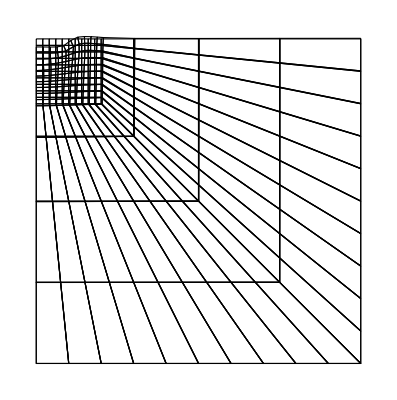

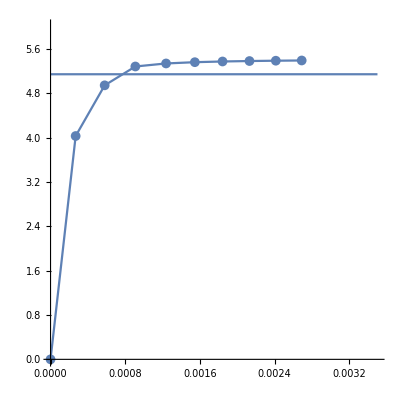

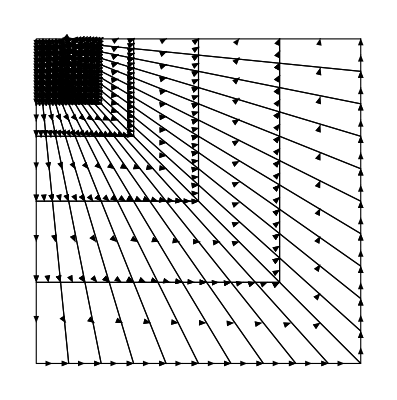

```mathematica
sim=5;
sol=solss[[sim]];
scale=100;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]
Show[ListLinePlot[(sol2//.subst2),AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[(2.+Pi),{x,0,0.0035}],PlotRange->{{0,0.0035},{0,6}}]
{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Arrowheads[.012],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
sh=Show[meshVis1,arrows,PlotRange->All]
```